# xSSA Example:SSAFit

LGPL Applies

```mathematica
<<xSSA.m;
```

xSSAlite 1.2.01 (1-March-2011) loaded Tue-8-Mar-2011-10:55:35 using Mathematica 8.0 for Linux x86 (64-bit) (November 7, 2010)(8.0.0)

```mathematica
r={{Overscript[A⇄B, P],2,1,.5,0}};
IC={A-> 100, P->100, B-> 0, A⋄P-> 0}; 
rsim=SSA[r,  10, IC, {}];
```

xSSA Exit. 603 steps.  602 points sampled.  0.06757 seconds.

```mathematica
fsim=SSAFit[rsim]
```

{A→InterpolatingFunction[{{0.,12.1657}},<>],B→InterpolatingFunction[{{0.,12.1657}},<>],P→InterpolatingFunction[{{0.,12.1657}},<>],A⋄P→InterpolatingFunction[{{0.,12.1657}},<>]}

This is the intteroplated data:

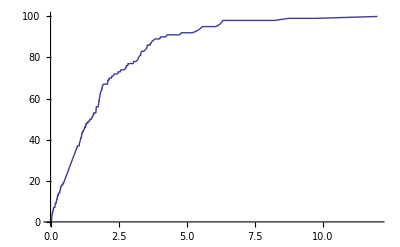

```mathematica
Plot[B[t]/.fsim, {t,0, 12.}]
```

This is the actual data:

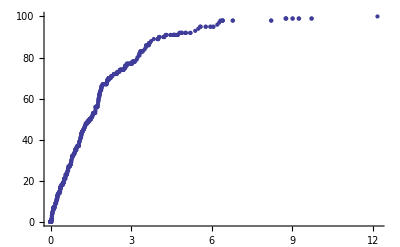

```mathematica
ListPlot[B/.rsim]
```